```mathematica
y1=m1 x;
y2=m2 x;
P=Log[x^2+y^2]/2;
primP=Simplify[Integrate[P,y]];
ρ=Simplify[(primP/.y->y2)-(primP/.y->y1)];
primPx=Integrate[D[P,x],y];
J=Simplify[(primPx/.y->y2)-(primPx/.y->y1)];
w=y2-y1;
σ=w;
a1=(P/.y->y1)D[y1,x];
a2=(P/.y->y2)D[y2,x];
p=ρ/w;
cD=Simplify[J w^2/((J-D[w,x]p+a2-a1))]
Simplify[cD/w^2]
```

(m1-m2) x^2 (ArcTan[m1]-ArcTan[m2])

(ArcTan[m1]-ArcTan[m2])/(m1-m2)

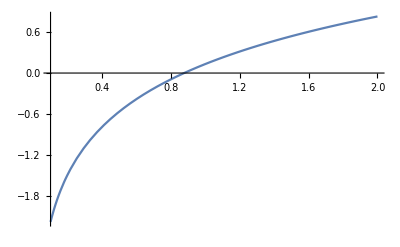

-Graphics3D-

```mathematica
sbs={m1->0,m2->1};
Plot[p/.sbs,{x,1/10,2}]
Plot3D[P,{x,-2,2},{y,-2,2}]
```

```mathematica
Simplify[J w / D[p,x]]
```

(m1-m2) x^2 (ArcTan[m1]-ArcTan[m2])

```mathematica
Simplify[w^2/D[w,x]]
```

-(m1-m2) x^2